7.97133

62.5421

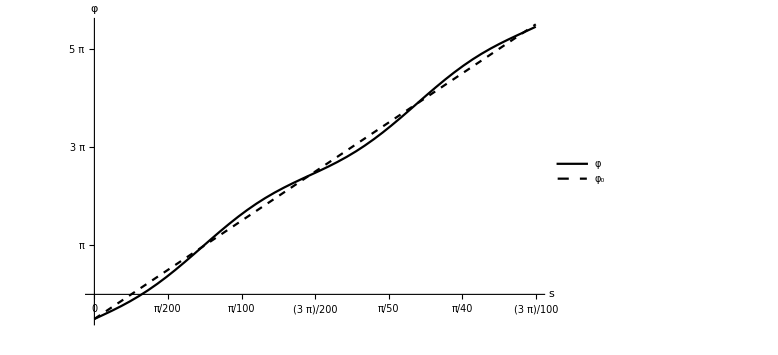

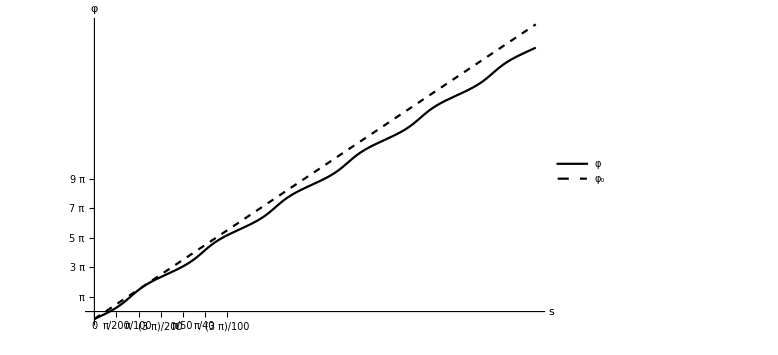

```mathematica
l=10^-2;
(*ω=0.99999999999999;
R=0.992;*)
ω=0.9921;
R=1;
γ=1/(1-R^2 ω^2)^(1/2)
α=R ω^2 γ^2
opts={Ticks->{Range[0,3Pi l,Pi l/2],Range[-Pi,10Pi,Pi]},AxesLabel->{"s","φ"},PlotStyle->{Black,{Black,Dashed}},ImageSize->Large,PlotLegends->{Text[Style["φ",16]],Text[Style["φ_0",16]]},AxesStyle->15};
fplus[s_]:=2 s/l-π/2-α  Sin[(2/l-ω γ^2)s]/(2/l-ω γ^2) 
plt1=Plot[{fplus[s],2 s/l-π/2},{s,0, 3Pi l},Evaluate[opts]]
rown=y'[s]-2/l-α Sin[y[s]-ω γ^2 s]==0;
sol=NDSolve[{rown,y[0]==-Pi/2},y[s],{s,0,50Pi l}];
(*opts1={Ticks->{Range[0,Pi/10,Pi/50],Range[-Pi,20Pi,5Pi]},AxesLabel->{"s","φ"},PlotStyle->{Black,{Black,Dashed}},ImageSize->Large,PlotLegends->{"φ","φ_0"}};*)
plt2=Plot[{y[s]/.sol,2 s/l-π/2},{s,0, 10Pi l},Evaluate[opts]]
```

```mathematica
Export["RAppW98R1L2.eps",plt1]
Export["RNumW98R1L2.eps",plt2]
```

RAppW98R1L2.eps

RNumW98R1L2.eps